```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/hybrid_metric-Palatini/math"];
```

## metric

```mathematica
coord={h1,h2,h3,h4};
n=Length[coord];
```

```mathematica
ΩΓ2=1+ξΓ Sum[coord[[i]]^2,{i,n}]
Ω2=1+ξg ΩΓ2^-1 Sum[coord[[i]]^2,{i,n}]
```

1+(h1^2+h2^2+h3^2+h4^2) ξΓ

1+((h1^2+h2^2+h3^2+h4^2) ξg)/(1+(h1^2+h2^2+h3^2+h4^2) ξΓ)

```mathematica
metric=DiagonalMatrix[Table[1/(Ω2 ΩΓ2),{j,n}]]+Table[coord[[i]]coord[[j]],{i,n},{j,n}](6 ξg^2/(Ω2^2 ΩΓ2^4)+6(ξg ξΓ)/(Ω2 ΩΓ2^2)(2-ξΓ/ΩΓ2 Sum[coord[[i]]^2,{i,n}]))//Simplify;
```

{{(h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+(1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ) (1+h4^2 ξg+h4^2 ξΓ+h2^2 (ξg+ξΓ)+h3^2 (ξg+ξΓ))+h1^2 (ξg+2 (6+h2^2+h3^2+h4^2) ξg ξΓ+6 (h2^2+h3^2+h4^2) ξg ξΓ^2+6 ξg^2 (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ) (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ))^2),(6 h1 h2 ξg (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ) (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ))^2),(6 h1 h3 ξg (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ) (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ))^2),(6 h1 h4 ξg (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ) (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ))^2)},{(6 h1 h2 ξg (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ) (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ))^2),(1+(h1^2+h2^2+h3^2+h4^2) ξg+(h1^2+h2^2+h3^2+h4^2) ξΓ+6 h2^2 ξg (ξg+(ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ))/(1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+(h1^2+h2^2+h3^2+h4^2) ξg+(h1^2+h2^2+h3^2+h4^2) ξΓ)^2),(6 h2 h3 ξg (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ) (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ))^2),(6 h2 h4 ξg (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ) (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ))^2)},{(6 h1 h3 ξg (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ) (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ))^2),(6 h2 h3 ξg (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ) (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ))^2),(1+(h1^2+h2^2+h3^2+h4^2) ξg+(h1^2+h2^2+h3^2+h4^2) ξΓ+6 h3^2 ξg (ξg+(ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ))/(1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+(h1^2+h2^2+h3^2+h4^2) ξg+(h1^2+h2^2+h3^2+h4^2) ξΓ)^2),(6 h3 h4 ξg (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ) (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ))^2)},{(6 h1 h4 ξg (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ) (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ))^2),(6 h2 h4 ξg (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ) (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ))^2),(6 h3 h4 ξg (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ) (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ))^2),(1+(h1^2+h2^2+h3^2+h4^2) ξg+(h1^2+h2^2+h3^2+h4^2) ξΓ+6 h4^2 ξg (ξg+(ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ))/(1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/((1+(h1^2+h2^2+h3^2+h4^2) ξg+(h1^2+h2^2+h3^2+h4^2) ξΓ)^2)}}

```mathematica
inversemetric=Simplify[Inverse[metric]]
```

{{((1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (6 (h2^2+h3^2+h4^2) ξg^2 ξΓ+2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h4^2 ξΓ+6 h4^2 ξΓ^2+2 h2^2 ξΓ (1+3 ξΓ)+2 h3^2 ξΓ (1+3 ξΓ)))))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ))),-((6 h1 h2 ξg (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ)))),-((6 h1 h3 ξg (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ)))),-((6 h1 h4 ξg (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ))))},{-((6 h1 h2 ξg (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ)))),((1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h2^4 ξΓ (ξg+ξΓ)+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (ξg+6 (h3^2+h4^2) ξg^2 ξΓ+2 h3^2 ξg ξΓ (1+3 ξΓ)+2 h4^2 ξg ξΓ (1+3 ξΓ)+2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ))+h1^2 (ξg+2 (6+h2^2+h3^2+h4^2) ξg ξΓ+6 (h2^2+2 (h3^2+h4^2)) ξg ξΓ^2+2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+6 ξg^2 (1+h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ))))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ))),-((6 h2 h3 ξg (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ)))),-((6 h2 h4 ξg (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ))))},{-((6 h1 h3 ξg (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ)))),-((6 h2 h3 ξg (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ)))),((1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (1+h3^2 ξg+h4^2 ξg+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (ξg+2 (6+h3^2+h4^2) ξg ξΓ+6 (h3^2+2 h4^2) ξg ξΓ^2+2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+6 ξg^2 (1+h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (ξg+2 (6+h2^2+h3^2+h4^2) ξg ξΓ+6 (2 h2^2+h3^2+2 h4^2) ξg ξΓ^2+2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+6 ξg^2 (1+2 h2^2 ξΓ+h3^2 ξΓ+2 h4^2 ξΓ))))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ))),-((6 h3 h4 ξg (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ))))},{-((6 h1 h4 ξg (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ)))),-((6 h2 h4 ξg (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ)))),-((6 h3 h4 ξg (1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (ξg (1+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξΓ (2+h1^2 ξΓ+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ)))),((1+h3^2 ξg+h4^2 ξg+h3^2 ξΓ+h4^2 ξΓ+h1^2 (ξg+ξΓ)+h2^2 (ξg+ξΓ)) (1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+6 h3^2 h4^2 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+6 h3^2 h4^2 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (ξg+2 (6+h3^2+h4^2) ξg ξΓ+6 (2 h3^2+h4^2) ξg ξΓ^2+2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+6 ξg^2 (1+2 h3^2 ξΓ+h4^2 ξΓ))+h1^2 (ξg+2 (6+h2^2+h3^2+h4^2) ξg ξΓ+6 (2 h2^2+2 h3^2+h4^2) ξg ξΓ^2+2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+6 ξg^2 (1+2 h2^2 ξΓ+2 h3^2 ξΓ+h4^2 ξΓ))))/(1+h3^2 ξg+h4^2 ξg+6 h3^2 ξg^2+6 h4^2 ξg^2+2 h3^2 ξΓ+2 h4^2 ξΓ+12 h3^2 ξg ξΓ+h3^4 ξg ξΓ+12 h4^2 ξg ξΓ+2 h3^2 h4^2 ξg ξΓ+h4^4 ξg ξΓ+6 h3^4 ξg^2 ξΓ+12 h3^2 h4^2 ξg^2 ξΓ+6 h4^4 ξg^2 ξΓ+h3^4 ξΓ^2+2 h3^2 h4^2 ξΓ^2+h4^4 ξΓ^2+6 h3^4 ξg ξΓ^2+12 h3^2 h4^2 ξg ξΓ^2+6 h4^4 ξg ξΓ^2+h1^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^4 (1+6 ξg) ξΓ (ξg+ξΓ)+h2^2 (1+6 ξg) (2 ξΓ (1+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h3^2 ξΓ+2 h4^2 ξΓ))+h1^2 (1+6 ξg) (2 ξΓ (1+h2^2 ξΓ+h3^2 ξΓ+h4^2 ξΓ)+ξg (1+2 h2^2 ξΓ+2 h3^2 ξΓ+2 h4^2 ξΓ)))}}

```mathematica
affine:=affine=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*(D[metric[[s,j]],coord[[k]]]+D[metric[[s,k]],coord[[j]]]-D[metric[[j,k]],coord[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]]
```

```mathematica
listaffine:=Table[If[UnsameQ[affine[[i,j,k]],0],{ToString[Γ[i,j,k]],affine[[i,j,k]]}],{i,1,n},{j,1,n},{k,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2,2}]
```

1
 |  |  |  |

```mathematica
riemann:=riemann=ParallelTable[Simplify[D[affine[[i,j,l]],coord[[k]]]-D[affine[[i,j,k]],coord[[l]]]+Sum[affine[[s,j,l]]affine[[i,k,s]]-affine[[s,j,k]]affine[[i,l,s]],{s,1,n}]],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]
```

```mathematica
listriemann:=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{ToString[R[i,j,k,l]],riemann[[i,j,k,l]]}],{i,1,n},{j,1,n},{k,1,n},{l,1,k-1}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listriemann],Null],2],TableSpacing->{2,2}]
```

1
 |  |  |  |

```mathematica
ricci:=ricci=ParallelTable[Sum[riemann[[i,j,i,l]],{i,1,n}]//Simplify,{j,1,n},{l,1,n}]
```

```mathematica
listricci:=Table[If[UnsameQ[ricci[[j,l]],0],{ToString[R[j,l]],ricci[[j,l]]}],{j,1,n},{l,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listricci],Null],2],TableSpacing->{2,2}]
```

1
 |  |  |  |

```mathematica
scalar=Simplify[Sum[inversemetric[[i,j]]ricci[[i,j]],{i,1,n},{j,1,n}]]/.{h1^2->h^2-h2^2-h3^2-h4^2,h1^4->(h^2-h2^2-h3^2-h4^2)^2,h1^6->(h^2-h2^2-h3^2-h4^2)^3,h1^8->(h^2-h2^2-h3^2-h4^2)^4}//FullSimplify
```

(6 (ξg (4+ξg (12+h^2 (1+6 ξg) (5+ξg (6+h^2 (1+6 ξg)))))+(1+6 ξg) (4+h^2 ξg (18+ξg (24+2 h^4 ξg (1+6 ξg)+h^2 (13+42 ξg)))) ξΓ+h^2 (1+6 ξg) (13+ξg (24+h^2 (27+ξg (84+h^4 ξg (1+6 ξg)+h^2 (11+54 ξg))))) ξΓ^2+h^4 (1+6 ξg) (15+ξg (48+3 h^4 ξg (1+6 ξg)+8 h^2 (2+9 ξg))) ξΓ^3+h^6 (1+6 ξg) (7+3 ξg (10+h^2 (1+6 ξg))) ξΓ^4+h^8 (1+6 ξg)^2 ξΓ^5))/(1+h^2 (1+6 ξg) (ξg+h^2 ξg ξΓ+ξΓ (2+h^2 ξΓ)))^2

```mathematica
scalar/.{h->0}//Expand
```

24 ξg+72 ξg^2+24 ξΓ+144 ξg ξΓ

```mathematica
Normal[Series[scalar,{h,∞,0}]]
```

6 (ξg+ξΓ)

```mathematica
Clear[ξΓsol]
```

```mathematica
ξΓsol[ξg_]=ξΓ/.Solve[2 10^-9==1/((1+6ξg)(ξg+ξΓ))(λ NN^2)/(12 π^2),ξΓ][[1]]
```

(125000000 NN^2 λ-3 π^2 ξg-18 π^2 ξg^2)/(3 π^2 (1+6 ξg))

```mathematica
Solve[ξΓsol[ξg]==0/.{NN->60,λ->1},ξg]//N
```

{{ξg→50329.1},{ξg→-50329.3}}

```mathematica
r[ξg_]=(1+6ξg)/(ξg+ξΓsol[ξg])2/NN^2/.{NN->60,λ->1}//Simplify
```

(π+6 π ξg)^2/270000000000000

## inf pheno

```mathematica
coord={h1,h2,h3,h4};
n=Length[coord];
```

```mathematica
ΩΓ2=1+ξΓ Sum[coord[[i]]^2,{i,n}]
Ω2=1+ξg ΩΓ2^-1 Sum[coord[[i]]^2,{i,n}]
```

1+(h1^2+h2^2+h3^2+h4^2) ξΓ

1+((h1^2+h2^2+h3^2+h4^2) ξg)/(1+(h1^2+h2^2+h3^2+h4^2) ξΓ)

```mathematica
metric=DiagonalMatrix[Table[1/(Ω2 ΩΓ2),{j,n}]]+Table[coord[[i]]coord[[j]],{i,n},{j,n}](6 ξg^2/(Ω2^2 ΩΓ2^4)+6(ξg ξΓ)/(Ω2 ΩΓ2^2)(2-ξΓ/ΩΓ2 Sum[coord[[i]]^2,{i,n}]))//Simplify;
```

```mathematica
metric/.{h1->x,h2->0,h3->0,h4->0}//Simplify
```

{{(1+x^4 (1+6 ξg) ξΓ (ξg+ξΓ)+x^2 (1+6 ξg) (ξg+2 ξΓ))/((1+x^2 ξΓ) (1+x^2 (ξg+ξΓ))^2),0,0,0},{0,1/(1+x^2 (ξg+ξΓ)),0,0},{0,0,1/(1+x^2 (ξg+ξΓ)),0},{0,0,0,1/(1+x^2 (ξg+ξΓ))}}

```mathematica
KK[x_]=Simplify[Eigenvalues[metric][[4]]]/.{h1^2->x^2-h2^2-h3^2-h4^2,h1^4->(x^2-h2^2-h3^2-h4^2)^2}//Simplify
```

(1+x^4 (1+6 ξg) ξΓ (ξg+ξΓ)+x^2 (1+6 ξg) (ξg+2 ξΓ))/((1+x^2 ξΓ) (1+x^2 (ξg+ξΓ))^2)

```mathematica
Eigenvalues[metric/.{h1->x/2,h2->x/2,h3->x/2,h4->x/2}//Simplify]//Simplify
```

{1/(1+x^2 (ξg+ξΓ)),1/(1+x^2 (ξg+ξΓ)),1/(1+x^2 (ξg+ξΓ)),(1+x^4 (1+6 ξg) ξΓ (ξg+ξΓ)+x^2 (1+6 ξg) (ξg+2 ξΓ))/((1+x^2 ξΓ) (1+x^2 (ξg+ξΓ))^2)}

```mathematica
Normal[Series[Sqrt[KK[x]],{x,0,2}]]
```

1+1/2 x^2 (-ξg+6 ξg^2-ξΓ+12 ξg ξΓ)

```mathematica
MinValue[{KK[x],x>0,ξg>0},x]
```

Piecewise[{{-∞, ξΓ<0&&ξg>0}, {0, ξΓ≥0&&ξg>0}, {∞, True}}]

```mathematica
Normal[Series[KK[x],{x,∞,6}]]
```

(-1-6 ξg)/(x^4 (ξg+ξΓ)^2)+(1+6 ξg)/(x^2 (ξg+ξΓ))+(-6 ξg^2+ξΓ)/(x^6 ξΓ (ξg+ξΓ)^3)

```mathematica
ξΓmin[ξg_]=ξΓ/.Solve[-ξg+6 ξg^2-ξΓ+12 ξg ξΓ==0,ξΓ][[1]]
```

(ξg-6 ξg^2)/(-1+12 ξg)

```mathematica
VV[x_]=x^4/(4 ΩΓ2^2 Ω2^2)/.{h1->x,h2->0,h3->0,h4->0}//Simplify;
ϵV[x_]=1/(2KK[x])(VV'[x]/VV[x])^2//Simplify;
ηV[x_]=1/(Sqrt[KK[x]]VV[x])D[VV'[x]/Sqrt[KK[x]], x]//Simplify;
```

```mathematica
HH[x_,p_]=Sqrt[(KK[x]/2 p^2+VV[x])/3];
ϵH[x_,p_]=(KK[x] p^2)/(2 HH[x,p]^2);
```

```mathematica
c3=ξg ξΓ^2+ξΓ^3+6 ξg^2 ξΓ^2+6ξg ξΓ^3;
c7=ξΓ^2(ξg+ξΓ)^2;
```

```mathematica
AA=Sqrt[c7/c3]//Simplify
```

√((ξg+ξΓ)/(1+6 ξg))

```mathematica
Normal[Series[VV[x],{x,∞,2}]]
```

-1/(2 x^2 (ξg+ξΓ)^3)+1/(4 (ξg+ξΓ)^2)

### sample

```mathematica
ξΓinξg[ξg_]=ξΓ/.Solve[1/((1+6ξg)(ξg+ξΓ))55^2/(12 π^2)==2 10^-9,ξΓ][[1]]
```

(378125000000-3 π^2 ξg-18 π^2 ξg^2)/(3 π^2 (1+6 ξg))

```mathematica
ξΓmin[10^3]
```

-5999000/11999

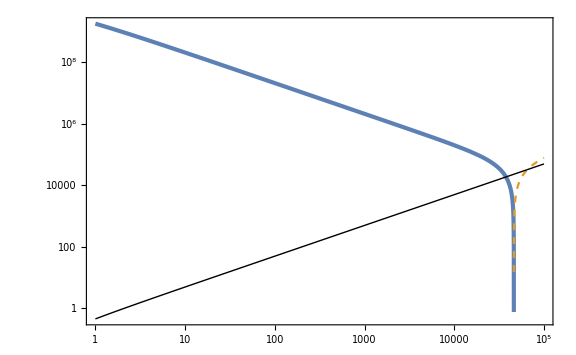

```mathematica
LogLogPlot[{ξΓinξg[ξg],-ξΓinξg[ξg],-ξΓmin[ξg]},{ξg,1,10^5},PlotStyle->{AbsoluteThickness[3],Dashed,{Thin,Black}}]
```

```mathematica
ξgs=10^5;
ξΓs=ξΓmin[ξgs];
xin=Sqrt[(8 AA^2)/(ξg+ξΓ)NN]/.{ξg->ξgs,ξΓ->ξΓs,NN->80};
Hin=HH[xin,0]/.{ξg->ξgs,ξΓ->ξΓs};
tf=500/Hin;
```

```mathematica
Sqrt[(8 AA^2)/(ξg+ξΓ)]/.{ξg->ξgs,ξΓ->ξΓs}//N
```

0.00365148

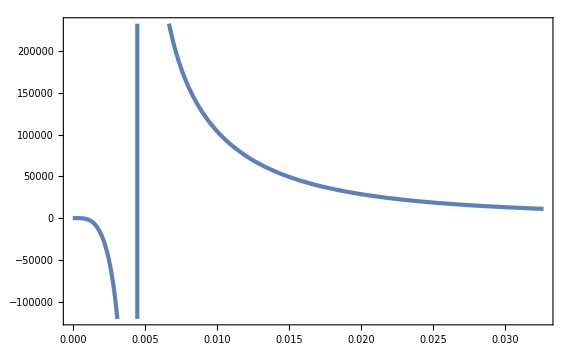

```mathematica
Plot[KK[x]/.{ξg->ξgs,ξΓ->ξΓs},{x,0,xin}]
```

```mathematica
χ[x_]:=NIntegrate[Sqrt[KK[xp]]/.{ξg->ξgs,ξΓ->ξΓs},{xp,0,x},WorkingPrecision->30];
```

```mathematica
χ[xin]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xp near {xp} = {0.00452886218611366257275370993543}. NIntegrate obtained 7.30872500973075681347684492748+1.54938059253313922862464637379 ⅈ and 0.191020197717880658031574211547 for the integral and error estimates.

7.30872500973075681347684492748+1.54938059253313922862464637379 ⅈ

```mathematica
sol=NDSolve[{x'[t]==UnitStep[1-ϵH[x[t],p[t]]]p[t],
p'[t]==-UnitStep[1-ϵH[x[t],p[t]]]((3HH[x[t],p[t]]+KK'[x[t]]/(2KK[x[t]])p[t])p[t]+VV'[x[t]]/KK[x[t]]),
x[0]==xin,p[0]==0,
NN'[t]==HH[x[t],p[t]],NN[0]==0,
tinf'[t]==UnitStep[1-ϵH[x[t],p[t]]],tinf[0]==0}/.{ξg->ξgs,ξΓ->ξΓs},{x[t],p[t],NN[t],tinf[t]},{t,0,tf},WorkingPrecision->50,MaxSteps->100000][[1]]
```

{x[t]→                                                                                 7
InterpolatingFunction[{{0, 8.8226340716869073965425069157090282294074715964099 10 }}, <>][t],p[t]→                                                                                 7
InterpolatingFunction[{{0, 8.8226340716869073965425069157090282294074715964099 10 }}, <>][t],NN[t]→                                                                                 7
InterpolatingFunction[{{0, 8.8226340716869073965425069157090282294074715964099 10 }}, <>][t],tinf[t]→                                                                                 7
InterpolatingFunction[{{0, 8.8226340716869073965425069157090282294074715964099 10 }}, <>][t]}

```mathematica
xsol[t_]=x[t]/.sol;
psol[t_]=p[t]/.sol;
Nsol[t_]=NN[t]/.sol;
Hsol[t_]=HH[xsol[t],psol[t]]/.{ξg->ξgs,ξΓ->ξΓs};
ϵHsol[t_]=ϵH[xsol[t],psol[t]]/.{ξg->ξgs,ξΓ->ξΓs};
ϵVsol[t_]=ϵV[xsol[t]]/.{ξg->ξgs,ξΓ->ξΓs};
ηVsol[t_]=ηV[xsol[t]]/.{ξg->ξgs,ξΓ->ξΓs};
tinfsol[t_]=tinf[t]/.sol;
```

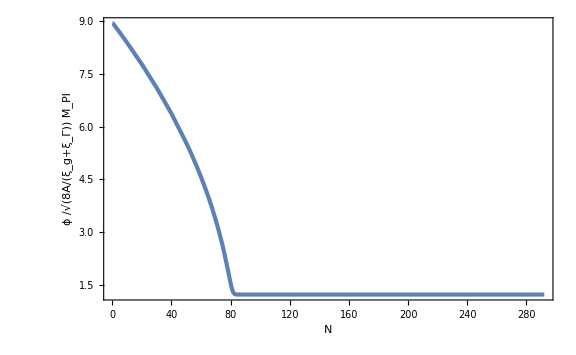

```mathematica
ParametricPlot[{Nsol[t],xsol[t]/Sqrt[(8 AA^2)/(ξg+ξΓ)]/.{ξg->ξgs,ξΓ->ξΓs}},{t,0,tf},PlotRange->Full,FrameLabel->{N,Row[{ϕ," /",Sqrt["8A/(ξ_g+ξ_Γ)"] Subscript[M, Pl]}]}]
```

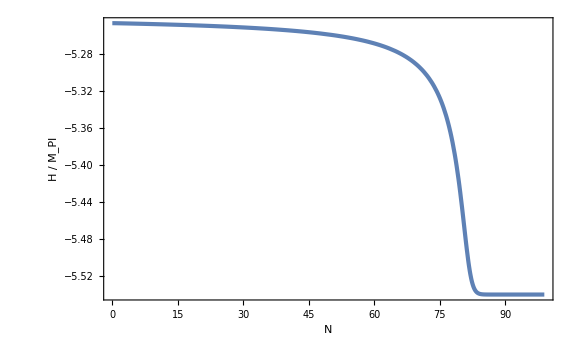

```mathematica
ParametricPlot[{Nsol[t],Log10[Hsol[t]]},{t,0,tf},PlotRange->Full,FrameLabel->{N,Row[{H," / ",Subscript[M, Pl]}]}]
```

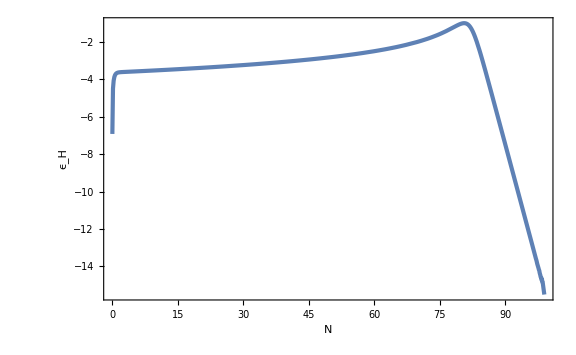

```mathematica
ParametricPlot[{Nsol[t],Log10[ϵHsol[t]]},{t,0,tf},FrameLabel->{N,Subscript[ϵ, H]}]
```

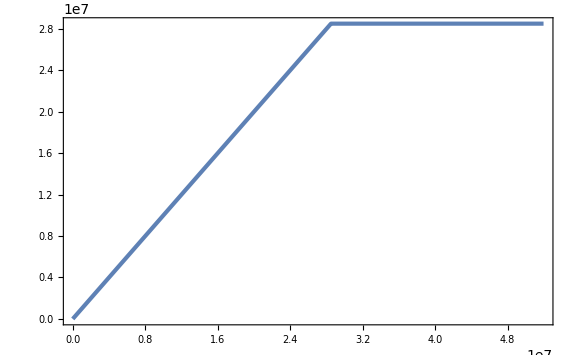

```mathematica
Plot[tinfsol[t],{t,0,tf}]
```

```mathematica
tend=tinfsol[tf]
Nend=Nsol[tend]
Ns=Nend-55
ts=t/.FindRoot[Nsol[t]==Ns,{t,1/4 tf},WorkingPrecision->30]
```

2.8501782309232901902760449448456241655729386127013×10^7

82.27751854029319594952016525230269800980543503249

27.27751854029319594952016525230269800980543503249

9.44921073789459862899288210613×10^6

```mathematica
tensor=16ϵVsol[ts]
ranal=(1+6ξg)/(ξg+ξΓ)2/NN^2/.{ξg->ξgs,ξΓ->ξΓs,NN->55}//N
```

7.4937834402645943314043699537×10^-9

7.00826×10^-9

```mathematica
calP=1/(24 π^2)VV[xsol[ts]]/ϵVsol[ts]/.{ξg->ξgs,ξΓ->ξΓs}
calPanal=1/((1+6ξg)(ξg+ξΓ))NN^2/(12 π^2)/.{ξg->ξgs,ξΓ->ξΓs,NN->55}//N
```

0.00022534491230333370983536704152

0.000240956

```mathematica
nsm1=-6ϵVsol[ts]+2ηVsol[ts]
nsm1anal=-2/55//N
```

-0.037602149083014374523545393748

-0.0363636

### param. search

```mathematica
AbsoluteTiming[ξgs=10^0;ξΓs=10^4;
xin=Sqrt[(8 AA^2)/(ξg+ξΓ)NN]/.{ξg->ξgs,ξΓ->ξΓs,NN->80};
Hin=HH[xin,0]/.{ξg->ξgs,ξΓ->ξΓs};
tf=150/Hin;
sol=NDSolve[{x'[t]==UnitStep[1-ϵH[x[t],p[t]]]p[t],
p'[t]==-UnitStep[1-ϵH[x[t],p[t]]]((3HH[x[t],p[t]]+KK'[x[t]]/(2KK[x[t]])p[t])p[t]+VV'[x[t]]/KK[x[t]]),
x[0]==xin,p[0]==0,
NN'[t]==HH[x[t],p[t]],NN[0]==0,
tinf'[t]==UnitStep[1-ϵH[x[t],p[t]]],tinf[0]==0}/.{ξg->ξgs,ξΓ->ξΓs},{x[t],p[t],NN[t],tinf[t]},{t,0,tf},WorkingPrecision->50,MaxSteps->100000][[1]];
xsol[t_]=x[t]/.sol;
psol[t_]=p[t]/.sol;
Nsol[t_]=NN[t]/.sol;
Hsol[t_]=HH[xsol[t],psol[t]]/.{ξg->ξgs,ξΓ->ξΓs};
ϵHsol[t_]=ϵH[xsol[t],psol[t]]/.{ξg->ξgs,ξΓ->ξΓs};
ϵVsol[t_]=ϵV[xsol[t]]/.{ξg->ξgs,ξΓ->ξΓs};
ηVsol[t_]=ηV[xsol[t]]/.{ξg->ξgs,ξΓ->ξΓs};
tinfsol[t_]=tinf[t]/.sol;
tend=tinfsol[tf];
Nend=Nsol[tend];
Ns=Nend-55;
ts=t/.FindRoot[Nsol[t]==Ns,{t,1/4 tf},WorkingPrecision->30];
{1/(24 π^2)VV[xsol[ts]]/ϵVsol[ts]/.{ξg->ξgs,ξΓ->ξΓs},1-6ϵVsol[ts]+2ηVsol[ts],16ϵVsol[ts]}]
```

{6.08852,{0.0003413722215886057460068634941,0.962407199750719008251393682127,4.9457543631613716154725551846×10^-7}}

```mathematica
calPnsrList=Table[ξgs=10^logξg;ξΓs=10^logξΓ;
xin=Sqrt[(8 AA^2)/(ξg+ξΓ)NN]/.{ξg->ξgs,ξΓ->ξΓs,NN->80};
Hin=HH[xin,0]/.{ξg->ξgs,ξΓ->ξΓs};
tf=150/Hin;
sol=NDSolve[{x'[t]==UnitStep[1-ϵH[x[t],p[t]]]p[t],
p'[t]==-UnitStep[1-ϵH[x[t],p[t]]]((3HH[x[t],p[t]]+KK'[x[t]]/(2KK[x[t]])p[t])p[t]+VV'[x[t]]/KK[x[t]]),
x[0]==xin,p[0]==0,
NN'[t]==HH[x[t],p[t]],NN[0]==0,
tinf'[t]==UnitStep[1-ϵH[x[t],p[t]]],tinf[0]==0}/.{ξg->ξgs,ξΓ->ξΓs},{x[t],p[t],NN[t],tinf[t]},{t,0,tf},WorkingPrecision->50,MaxSteps->100000][[1]];
xsol[t_]=x[t]/.sol;
psol[t_]=p[t]/.sol;
Nsol[t_]=NN[t]/.sol;
Hsol[t_]=HH[xsol[t],psol[t]]/.{ξg->ξgs,ξΓ->ξΓs};
ϵHsol[t_]=ϵH[xsol[t],psol[t]]/.{ξg->ξgs,ξΓ->ξΓs};
ϵVsol[t_]=ϵV[xsol[t]]/.{ξg->ξgs,ξΓ->ξΓs};
ηVsol[t_]=ηV[xsol[t]]/.{ξg->ξgs,ξΓ->ξΓs};
tinfsol[t_]=tinf[t]/.sol;
tend=tinfsol[tf];
Nend=Nsol[tend];
Ns=Nend-55;
ts=t/.FindRoot[Nsol[t]==Ns,{t,1/4 tf},WorkingPrecision->30];
{ξgs,ξΓs,1/(24 π^2)VV[xsol[ts]]/ϵVsol[ts]/.{ξg->ξgs,ξΓ->ξΓs},1-6ϵVsol[ts]+2ηVsol[ts],16ϵVsol[ts]},{logξg,-2,5},{logξΓ,-2,10}];//AbsoluteTiming
```

{534.02,Null}

```mathematica
Export["calPnsr.dat",Flatten[calPnsrList,1]];
```

```mathematica
calPnsrList=Import["calPnsr.dat"]//ToExpression;
```

```mathematica
LogcalPList=Map[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]]}&,calPnsrList];
LogrList=Map[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[5]]]}&,calPnsrList];
nsList=Map[{Log10[#[[1]]],Log10[#[[2]]],#[[4]]}&,calPnsrList];
```

```mathematica
LogcalPint[logξg_,logξΓ_]=Interpolation[LogcalPList][logξg,logξΓ];
Logrint[logξg_,logξΓ_]=Interpolation[LogrList][logξg,logξΓ];
nsint[logξg_,logξΓ_]=Interpolation[nsList][logξg,logξΓ];
```

```mathematica
Clear[calPanal,ranal]
calPanal[ξg_,ξΓ_]=1/((1+6ξg)(ξg+ξΓ))55^2/(12 π^2);
ranal[ξg_,ξΓ_]=(1+6ξg)/(ξg+ξΓ)2/55^2;
```

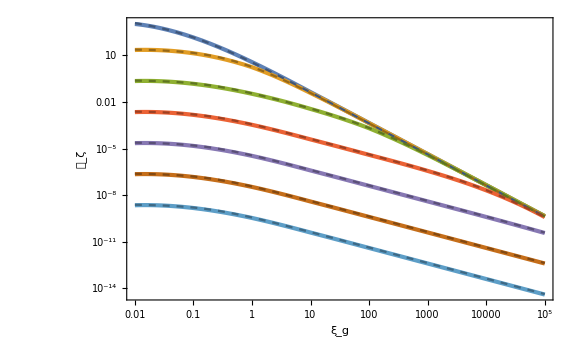

```mathematica
LogLogPlot[{10^LogcalPint[Log10[ξg],-2],10^LogcalPint[Log10[ξg],0],10^LogcalPint[Log10[ξg],2],10^LogcalPint[Log10[ξg],4],10^LogcalPint[Log10[ξg],6],10^LogcalPint[Log10[ξg],8],10^LogcalPint[Log10[ξg],10],calPanal[ξg,10^-2],calPanal[ξg,10^0],calPanal[ξg,10^2],calPanal[ξg,10^4],calPanal[ξg,10^6],calPanal[ξg,10^8],calPanal[ξg,10^10]},{ξg,10^-2,10^5},PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Darker[Color[1]],Dashed},{Darker[Color[2]],Dashed},{Darker[Color[3]],Dashed},{Darker[Color[4]],Dashed},{Darker[Color[5]],Dashed},{Darker[Color[6]],Dashed},{Darker[Color[7]],Dashed}},FrameLabel->{{Subscript[𝒫, ζ],None},{Subscript[ξ, g],Row[{λ==1,", ",N==55}]}}]
```

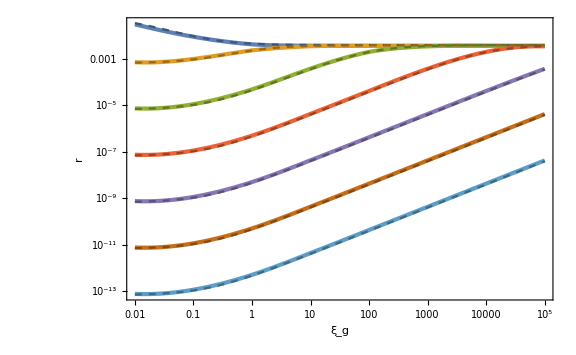

```mathematica
LogLogPlot[{10^Logrint[Log10[ξg],-2],10^Logrint[Log10[ξg],0],10^Logrint[Log10[ξg],2],10^Logrint[Log10[ξg],4],10^Logrint[Log10[ξg],6],10^Logrint[Log10[ξg],8],10^Logrint[Log10[ξg],10],ranal[ξg,10^-2],ranal[ξg,10^0],ranal[ξg,10^2],ranal[ξg,10^4],ranal[ξg,10^6],ranal[ξg,10^8],ranal[ξg,10^10]},{ξg,10^-2,10^5},PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Darker[Color[1]],Dashed},{Darker[Color[2]],Dashed},{Darker[Color[3]],Dashed},{Darker[Color[4]],Dashed},{Darker[Color[5]],Dashed},{Darker[Color[6]],Dashed},{Darker[Color[7]],Dashed}},FrameLabel->{{r,None},{Subscript[ξ, g],Row[{λ==1,", ",N==55}]}}]
```

```mathematica
Clear[n]
```

```mathematica
nsanal[ξg_,ξΓ_]=1-2/55-6/(8AA 55^2)
```

53/55-3/(12100 √((ξg+ξΓ)/(1+6 ξg)))

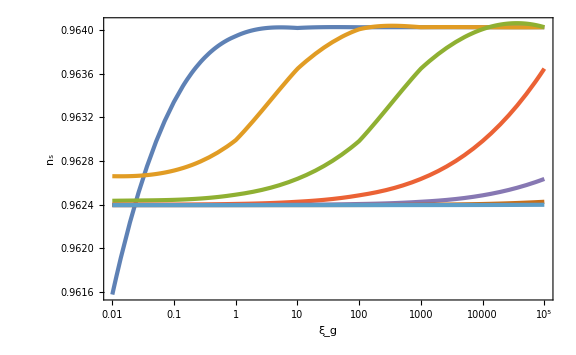

```mathematica
LogLinearPlot[{nsint[Log10[ξg],-2],nsint[Log10[ξg],0],nsint[Log10[ξg],2],nsint[Log10[ξg],4],nsint[Log10[ξg],6],nsint[Log10[ξg],8],nsint[Log10[ξg],10]},{ξg,10^-2,10^5},PlotRange->Full,GridLines->{None,{1-2/55}},FrameLabel->{{Subscript[n, "s"],None},{Subscript[ξ, g],Row[{λ==1,", ",N==55}]}}]
```

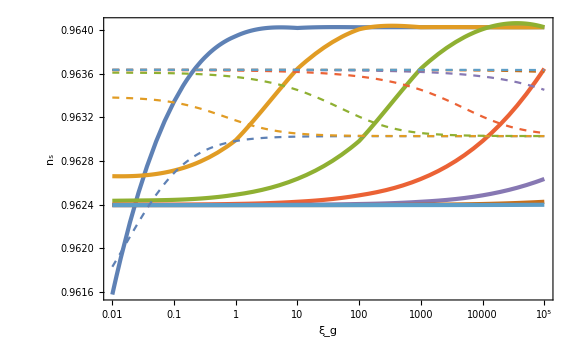

```mathematica
LogLinearPlot[{nsint[Log10[ξg],-2],nsint[Log10[ξg],0],nsint[Log10[ξg],2],nsint[Log10[ξg],4],nsint[Log10[ξg],6],nsint[Log10[ξg],8],nsint[Log10[ξg],10],nsanal[ξg,10^-2],nsanal[ξg,10^0],nsanal[ξg,10^2],nsanal[ξg,10^4],nsanal[ξg,10^6],nsanal[ξg,10^8],nsanal[ξg,10^10]},{ξg,10^-2,10^5},PlotRange->Full(*,GridLines->{None,{1-2/55}}*),FrameLabel->{{Subscript[n, "s"],None},{Subscript[ξ, g],Row[{λ==1,", ",N==55}]}},PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Color[1],Dashed},{Color[2],Dashed},{Color[3],Dashed},{Color[4],Dashed},{Color[5],Dashed},{Color[6],Dashed},{Color[7],Dashed}}]
```

## metric w/ EH

```mathematica
coord={h1,h2,h3,h4};
n=Length[coord];
```

```mathematica
metric=1/((1+(ξg+ξΓ)Sum[coord[[i]]^2,{i,n}]/Mp^2)^2)1/(MΓ^2+ξΓ Sum[coord[[i]]^2,{i,n}])Table[(1+(ξg+ξΓ)Sum[coord[[s]]^2,{s,n}]/Mp^2)(MΓ^2+ξΓ Sum[coord[[s]]^2,{s,n}])KroneckerDelta[i,j]+6((MΓ^2/Mp^2-1)ξΓ^2+ξg(2ξΓ+ξg)MΓ^2/Mp^2+ξΓ ξg(ξg+ξΓ)Sum[coord[[s]]^2,{s,n}]/Mp^2)coord[[i]]coord[[j]],{i,n},{j,n}]//Simplify
```

{{(1+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp^2+(6 h1^2 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/(Mp^2 (MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ)))/((1+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp^2)^2),(6 h1 h2 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/((MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ) (Mp+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp)^2),(6 h1 h3 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/((MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ) (Mp+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp)^2),(6 h1 h4 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/((MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ) (Mp+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp)^2)},{(6 h1 h2 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/((MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ) (Mp+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp)^2),(1+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp^2+(6 h2^2 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/(Mp^2 (MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ)))/((1+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp^2)^2),(6 h2 h3 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/((MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ) (Mp+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp)^2),(6 h2 h4 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/((MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ) (Mp+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp)^2)},{(6 h1 h3 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/((MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ) (Mp+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp)^2),(6 h2 h3 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/((MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ) (Mp+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp)^2),(1+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp^2+(6 h3^2 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/(Mp^2 (MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ)))/((1+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp^2)^2),(6 h3 h4 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/((MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ) (Mp+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp)^2)},{(6 h1 h4 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/((MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ) (Mp+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp)^2),(6 h2 h4 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/((MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ) (Mp+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp)^2),(6 h3 h4 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/((MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ) (Mp+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp)^2),(1+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp^2+(6 h4^2 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/(Mp^2 (MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ)))/((1+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp^2)^2)}}

```mathematica
inversemetric=Simplify[Inverse[metric]]
```

{{((Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (Mp^2 (MΓ^2+ξΓ (h1^2-(h2^2+h3^2+h4^2) (-1+6 ξΓ)))+(ξg+ξΓ) (h1^4 ξΓ+h1^2 (MΓ^2+2 (h2^2+h3^2+h4^2) (1+3 ξg) ξΓ)+(h2^2+h3^2+h4^2) ((h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ))),-((6 h1 h2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (MΓ^2 (ξg+ξΓ)^2+ξΓ (h3^2 ξg^2+h4^2 ξg^2-Mp^2 ξΓ+h3^2 ξg ξΓ+h4^2 ξg ξΓ+h1^2 ξg (ξg+ξΓ)+h2^2 ξg (ξg+ξΓ))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))),-((6 h1 h3 (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (MΓ^2 (ξg+ξΓ)^2+ξΓ (h3^2 ξg^2+h4^2 ξg^2-Mp^2 ξΓ+h3^2 ξg ξΓ+h4^2 ξg ξΓ+h1^2 ξg (ξg+ξΓ)+h2^2 ξg (ξg+ξΓ))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))),-((6 h1 h4 (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (MΓ^2 (ξg+ξΓ)^2+ξΓ (h3^2 ξg^2+h4^2 ξg^2-Mp^2 ξΓ+h3^2 ξg ξΓ+h4^2 ξg ξΓ+h1^2 ξg (ξg+ξΓ)+h2^2 ξg (ξg+ξΓ))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ))))},{-((6 h1 h2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (MΓ^2 (ξg+ξΓ)^2+ξΓ (h3^2 ξg^2+h4^2 ξg^2-Mp^2 ξΓ+h3^2 ξg ξΓ+h4^2 ξg ξΓ+h1^2 ξg (ξg+ξΓ)+h2^2 ξg (ξg+ξΓ))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))),-(((Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (-Mp^2 (MΓ^2+ξΓ (h2^2+h1^2 (1-6 ξΓ)-(h3^2+h4^2) (-1+6 ξΓ)))-(ξg+ξΓ) (h2^4 ξΓ+h1^4 (ξΓ+6 ξg ξΓ)+h2^2 (MΓ^2+2 (h3^2+h4^2) (1+3 ξg) ξΓ)+(h3^2+h4^2) ((h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ))+h1^2 (2 (h2^2 (1+3 ξg)+(h3^2+h4^2) (1+6 ξg)) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))),-((6 h2 h3 (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (MΓ^2 (ξg+ξΓ)^2+ξΓ (h3^2 ξg^2+h4^2 ξg^2-Mp^2 ξΓ+h3^2 ξg ξΓ+h4^2 ξg ξΓ+h1^2 ξg (ξg+ξΓ)+h2^2 ξg (ξg+ξΓ))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))),-((6 h2 h4 (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (MΓ^2 (ξg+ξΓ)^2+ξΓ (h3^2 ξg^2+h4^2 ξg^2-Mp^2 ξΓ+h3^2 ξg ξΓ+h4^2 ξg ξΓ+h1^2 ξg (ξg+ξΓ)+h2^2 ξg (ξg+ξΓ))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ))))},{-((6 h1 h3 (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (MΓ^2 (ξg+ξΓ)^2+ξΓ (h3^2 ξg^2+h4^2 ξg^2-Mp^2 ξΓ+h3^2 ξg ξΓ+h4^2 ξg ξΓ+h1^2 ξg (ξg+ξΓ)+h2^2 ξg (ξg+ξΓ))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))),-((6 h2 h3 (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (MΓ^2 (ξg+ξΓ)^2+ξΓ (h3^2 ξg^2+h4^2 ξg^2-Mp^2 ξΓ+h3^2 ξg ξΓ+h4^2 ξg ξΓ+h1^2 ξg (ξg+ξΓ)+h2^2 ξg (ξg+ξΓ))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))),-(((Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (-Mp^2 (MΓ^2+ξΓ (h2^2+h3^2+h4^2+h1^2 (1-6 ξΓ)-6 h2^2 ξΓ-6 h4^2 ξΓ))-(ξg+ξΓ) (h3^2 MΓ^2+h4^2 MΓ^2+6 h4^2 MΓ^2 ξg+h3^4 ξΓ+2 h3^2 h4^2 ξΓ+h4^4 ξΓ+6 h4^2 MΓ^2 ξΓ+6 h3^2 h4^2 ξg ξΓ+6 h4^4 ξg ξΓ+h1^4 (ξΓ+6 ξg ξΓ)+h2^4 (ξΓ+6 ξg ξΓ)+h2^2 (2 (h3^2+h4^2+3 h3^2 ξg+6 h4^2 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ))+h1^2 (2 (h2^2+h3^2+h4^2+6 h2^2 ξg+3 h3^2 ξg+6 h4^2 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))),-((6 h3 h4 (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (MΓ^2 (ξg+ξΓ)^2+ξΓ (h3^2 ξg^2+h4^2 ξg^2-Mp^2 ξΓ+h3^2 ξg ξΓ+h4^2 ξg ξΓ+h1^2 ξg (ξg+ξΓ)+h2^2 ξg (ξg+ξΓ))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ))))},{-((6 h1 h4 (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (MΓ^2 (ξg+ξΓ)^2+ξΓ (h3^2 ξg^2+h4^2 ξg^2-Mp^2 ξΓ+h3^2 ξg ξΓ+h4^2 ξg ξΓ+h1^2 ξg (ξg+ξΓ)+h2^2 ξg (ξg+ξΓ))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))),-((6 h2 h4 (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (MΓ^2 (ξg+ξΓ)^2+ξΓ (h3^2 ξg^2+h4^2 ξg^2-Mp^2 ξΓ+h3^2 ξg ξΓ+h4^2 ξg ξΓ+h1^2 ξg (ξg+ξΓ)+h2^2 ξg (ξg+ξΓ))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))),-((6 h3 h4 (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (MΓ^2 (ξg+ξΓ)^2+ξΓ (h3^2 ξg^2+h4^2 ξg^2-Mp^2 ξΓ+h3^2 ξg ξΓ+h4^2 ξg ξΓ+h1^2 ξg (ξg+ξΓ)+h2^2 ξg (ξg+ξΓ))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))),-(((Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (-Mp^2 (MΓ^2+ξΓ (h2^2+h3^2+h4^2+h1^2 (1-6 ξΓ)-6 h2^2 ξΓ-6 h3^2 ξΓ))-(ξg+ξΓ) (h3^2 MΓ^2+h4^2 MΓ^2+6 h3^2 MΓ^2 ξg+h3^4 ξΓ+2 h3^2 h4^2 ξΓ+h4^4 ξΓ+6 h3^2 MΓ^2 ξΓ+6 h3^4 ξg ξΓ+6 h3^2 h4^2 ξg ξΓ+h1^4 (ξΓ+6 ξg ξΓ)+h2^4 (ξΓ+6 ξg ξΓ)+h2^2 (2 (h3^2+h4^2+6 h3^2 ξg+3 h4^2 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ))+h1^2 (2 (h2^2+h3^2+h4^2+6 h2^2 ξg+6 h3^2 ξg+3 h4^2 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ))))}}

```mathematica
affine:=affine=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*(D[metric[[s,j]],coord[[k]]]+D[metric[[s,k]],coord[[j]]]-D[metric[[j,k]],coord[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]]
```

```mathematica
listaffine:=Table[If[UnsameQ[affine[[i,j,k]],0],{ToString[Γ[i,j,k]],affine[[i,j,k]]}],{i,1,n},{j,1,n},{k,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2,2}]
```

1
 |  |  |  |

```mathematica
riemann:=riemann=ParallelTable[Simplify[D[affine[[i,j,l]],coord[[k]]]-D[affine[[i,j,k]],coord[[l]]]+Sum[affine[[s,j,l]]affine[[i,k,s]]-affine[[s,j,k]]affine[[i,l,s]],{s,1,n}]],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]
```

```mathematica
riemann
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

$Aborted

```mathematica
listriemann:=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{ToString[R[i,j,k,l]],riemann[[i,j,k,l]]}],{i,1,n},{j,1,n},{k,1,n},{l,1,k-1}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listriemann],Null],2],TableSpacing->{2,2}]
```

$Aborted

```mathematica
ricci:=ricci=Table[Sum[riemann[[i,j,i,l]],{i,1,n}]//Simplify,{j,1,n},{l,1,n}]
```

```mathematica
listricci:=Table[If[UnsameQ[ricci[[j,l]],0],{ToString[R[j,l]],ricci[[j,l]]}],{j,1,n},{l,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listricci],Null],2],TableSpacing->{2,2}]
```

1
 |  |  |  |

```mathematica
scalar=Simplify[Sum[inversemetric[[i,j]]ricci[[i,j]],{i,1,n},{j,1,n}]]/.{h1^2->h^2-h2^2-h3^2-h4^2,h1^4->(h^2-h2^2-h3^2-h4^2)^2,h1^6->(h^2-h2^2-h3^2-h4^2)^3,h1^8->(h^2-h2^2-h3^2-h4^2)^4}//FullSimplify
```

(6 (ξg (4+ξg (12+h^2 (1+6 ξg) (5+ξg (6+h^2 (1+6 ξg)))))+(1+6 ξg) (4+h^2 ξg (18+ξg (24+2 h^4 ξg (1+6 ξg)+h^2 (13+42 ξg)))) ξΓ+h^2 (1+6 ξg) (13+ξg (24+h^2 (27+ξg (84+h^4 ξg (1+6 ξg)+h^2 (11+54 ξg))))) ξΓ^2+h^4 (1+6 ξg) (15+ξg (48+3 h^4 ξg (1+6 ξg)+8 h^2 (2+9 ξg))) ξΓ^3+h^6 (1+6 ξg) (7+3 ξg (10+h^2 (1+6 ξg))) ξΓ^4+h^8 (1+6 ξg)^2 ξΓ^5))/(1+h^2 (1+6 ξg) (ξg+h^2 ξg ξΓ+ξΓ (2+h^2 ξΓ)))^2

```mathematica
scalar/.{h->0}//Expand
```

24 ξg+72 ξg^2+24 ξΓ+144 ξg ξΓ

```mathematica
Normal[Series[scalar,{h,∞,0}]]
```

6 (ξg+ξΓ)